## SDE求解

对于随机微分方程 dx = μ dt + σ dW,  其迭代式为：
-Graphics-
这里取μ = sin(t) 以及 σ = 10，其中ξ 服从正态分布N(0,dt). 我们取10000个系综，并设置时间精度为0.01，时间长度为5，利用上述的迭代式，会有如下的程序：

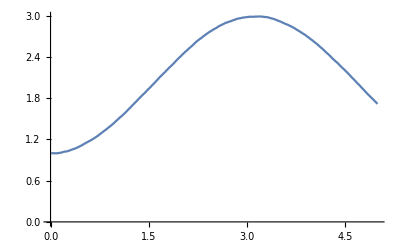

```mathematica
Clear["Global`*"]
en=10000;(*系综*)
dt=0.01;t=5;(*时间*)
(*参数*)
len=IntegerPart[t/dt];
x0=1;(*初始条件*)
mu=Table[Sin[i*dt],{i,1,len}];(*时间变化*)
sigma=Table[10,{i,1,len}];(*方差*)
tlist=Table[dt*n,{n,1,len}];(*时间标号*)
Xlist=Table[0,len,en];(*x(t)标号*)

Table[{x=x0;xlist=Table[0,len];(*初始化x*)
list=RandomVariate[NormalDistribution[0,dt],len];(*产生随机参数*)
Table[{x=x+mu[[n]]*dt+sigma[[n]]*list[[n]],xlist[[n]]=x},{n,1,len}];(*迭代*)
Table[Xlist[[i,j]]=Xlist[[i,j]]+xlist[[i]],{i,1,len}];(*收集当前系统的解*)
},{j,1,en}];
Table[xlist[[i]]=xlist[[i]]+Xlist[[i,j]];,{j,1,en},{i,1,len}];
xlist=xlist/en;
Transpose[{tlist,xlist}]//ListLinePlot
```

上图输出的结果为取了系综平均之后方程的解，可见这与没有方差的解基本一致，下面统计一下在某个时间点，x的分布直方图：

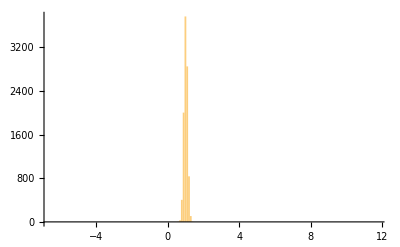
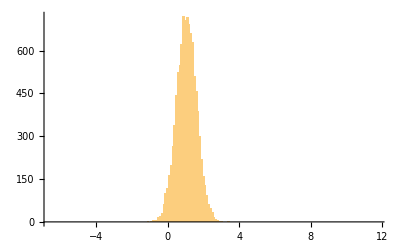
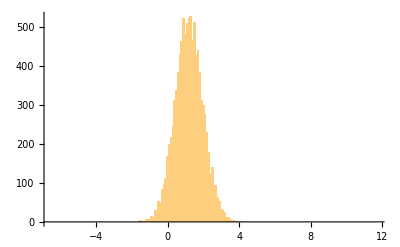
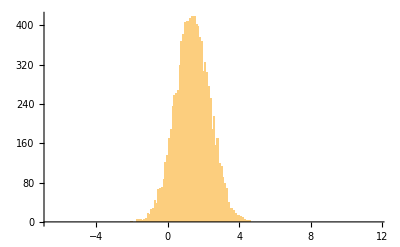
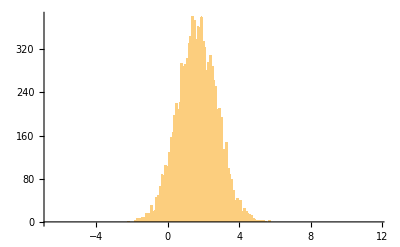
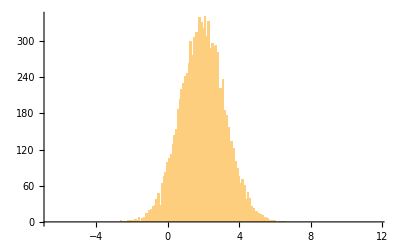
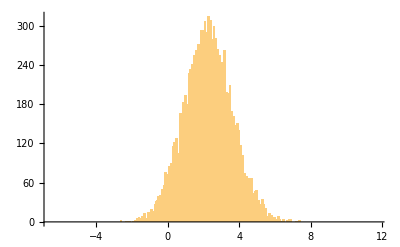
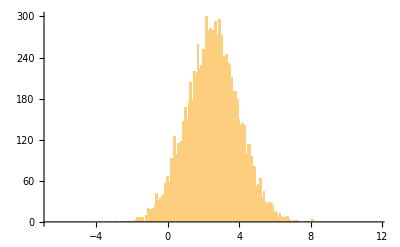

```mathematica
Table[Histogram[Xlist[[i]],{Min[Xlist],Max[Xlist],0.1}],{i,1,len,30}]
```

可见，随着时间的增加，刚开始的分布类似于delta函数，之后逐渐扩散，形成越来越宽的高斯波包状的分布，并且方差越来越大。